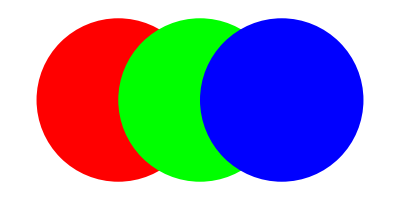

```mathematica
Graphics[GraphicsGroup[{Red,Disk[{0,0}],GraphicsGroup[{Green,Disk[{1,0}],GraphicsGroup[{Blue,Disk[{2,0}]}]}]}]]
```

```mathematica
Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},Filling->Axis]
```

-Graphics-

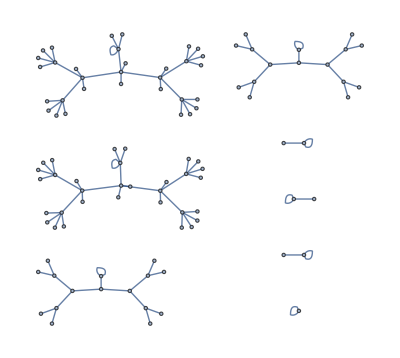

```mathematica
GraphPlot[Table[i->Mod[i^2,102],{i,0,102}]]
```

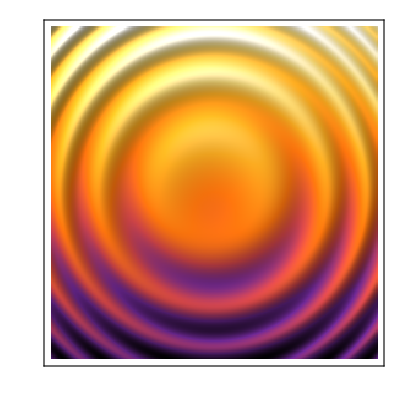

```mathematica
ReliefPlot[Table[i+Sin[i^2+j^2],{i,-4,4,.03},{j,-4,4,.03}],ColorFunction->"SunsetColors"]
```

```mathematica
ParametricPlot[{(v+u) Cos[u],(v+u) Sin[u]},{u,0,4 Pi},{v,0,5},Mesh->False]
```

-Graphics-

```mathematica
ContourPlot[y+Sin[x^2+3 y],{x,-3,3},{y,-3,3},ColorFunction->"Rainbow"]
```

-Graphics-

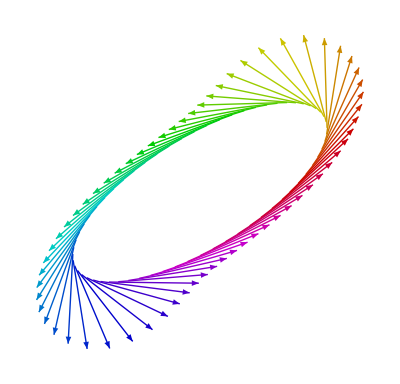

```mathematica
With[{f={Cos[x]+Sin[x],Sin[x]}},Graphics[Table[{Hue[t/(2Pi),1,.8],Arrow[{f,Normalize[D[f,x]]+f}]}/.x->t,{t,0,2Pi,.1}]]]
```

```mathematica
Plot[Sin[x], {x, 0, 6 Pi}]
```

-Graphics-

```mathematica
Rasterize[Cell["Mathematica", "ExampleText", FontSize -> 12]]
```

-Graphics-

```mathematica
Plot[{Sin[x], Sin[2 x], Sin[3 x]}, {x, 0, 2 Pi},PlotLegends -> "Expressions"]
```

-Graphics-

```mathematica
ListPlot[Table[{k, PDF[BinomialDistribution[50, p], k]}, {p, {0.3, 0.5, 0.8}}, {k, 0, 50}], Filling -> Axis, PlotLegends -> {0.3, 0.5, 0.8}]
```

-Graphics-

```mathematica
Show[DiscretePlot[Sin[t], {t, 0, 2 Pi, Pi/6}, ExtentSize -> Full], Plot[Sin[t], {t, 0, 2 Pi}]]
```

-Graphics-

```mathematica
DensityPlot[Sin[x] Sin[y], {x, -4, 4}, {y, -3, 3}, ColorFunction -> "SunsetColors", PlotLegends -> Automatic]
```

-Graphics-

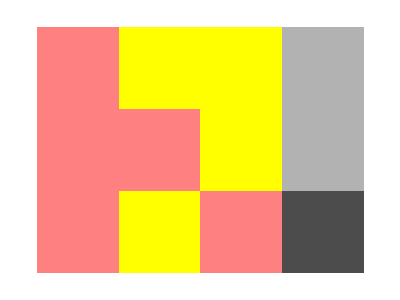

```mathematica
ArrayPlot[{{1, 0, 0, 0.3}, {1, 1, 0, 0.3}, {1, 0, 1, 0.7}}, ColorRules -> {1 -> Pink, 0 -> Yellow}]
```

```mathematica
RegionPlot[Sin[x] Sin[y] > 1/4, {x, -10, 10}, {y, -10, 10}, BoundaryStyle -> Dashed, PlotStyle -> Yellow]
```

-Graphics-

```mathematica
Import["ExampleData/spikey.tiff"]
```

-Graphics-

```mathematica
Manipulate[Plot[Sin[a x], {x, 0, 6}], {a, 1, 5}]
```

```mathematica
GraphicsBox[{InsetBox[BoxData[FormBox[PaneBox[DynamicBox[FEPrivate`FrontEndResource["MUnitExpressions","SuccessIcon"]],Alignment->Center,ImageSize->Dynamic[{Automatic,3.5CurrentValue["FontCapHeight"]/AbsoluteCurrentValue[Magnification]}]],TraditionalForm]]]}, PlotRange->{{0,1},{0,1}},Background->GrayLevel[0.93],Axes->False,AspectRatio->1,ImageSize->Dynamic[{Automatic, 3.5 CurrentValue["FontCapHeight"]/AbsoluteCurrentValue[Magnification]}],Frame->True,FrameTicks->None,FrameStyle->Directive[Thickness[Tiny],GrayLevel[0.55]]]//RawBoxes
```

-Graphics-

```mathematica
GraphicsBox[DynamicModuleBox[{p={RectangleBox[{-10,-25},{74,67}]}},DynamicBox[{p}]]]//RawBoxes
```

-Graphics-

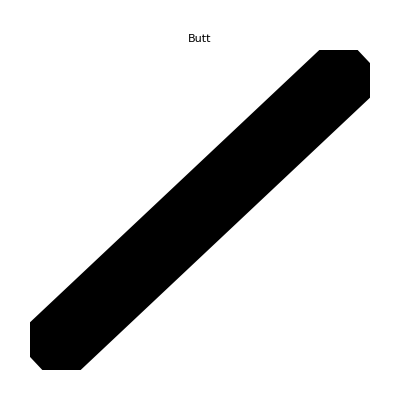
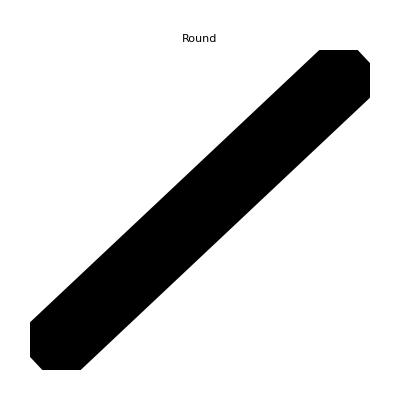
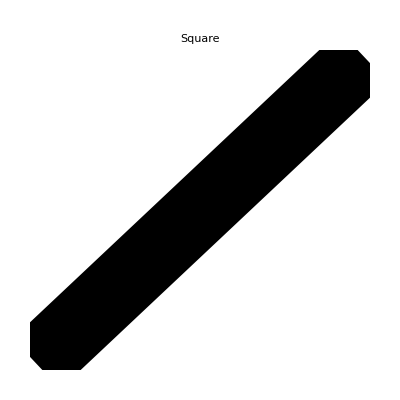

```mathematica
Table[Graphics[{CapForm[cap],Thickness[.2],Line[{{-1,-1},{1,1}}]},PlotRange->1.5,PlotLabel->cap],{cap,{"Butt","Round","Square"}}]
```

```mathematica
Manipulate[GraphicsRow[{Show[Plot[Sin[x],{x,-8,8},PlotStyle->Thickness[.007],ImageSize->Scaled[.7],PlotRange->{{-8,12},{-2,2}},Epilog->Inset[Row[{"Some Text"}],{10,0}]]]}],{dummy,0,1}]
```

```mathematica
Graphics[{},ImageSize->{2,0}]
```

-Graphics-

```mathematica
RowBox[{"a",GraphicsBox[{},ImageSize->{2,0}],"b"}]//RawBoxes
```

a-Graphics-b

```mathematica
Manipulate[Graphics[{Red,Disk[{0,a}]},PlotRange->{{-2,2},{-2,2}},Epilog->{Blue,Dynamic[Disk[{1,a}]]}],{a,0,1}]
```